Definicje funkcji używanych przy mapowaniu:

```mathematica
GetMax[x_] :={First[x], Max[Take[x,{2,Length[x]}]]};
```

```mathematica
GetMean[x_] :={First[x], Mean[Take[x,{2,Length[x]}]]};
```

```mathematica
GetVariance[x_] :={First[x], Variance[Take[x,{2,Length[x]}]]};
```

```mathematica
GetPlusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] + StandardDeviation[Take[x,{2,Length[x]}]]};
```

```mathematica
GetMinusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] - StandardDeviation[Take[x,{2,Length[x]}]]};
```

Pobieranie danych i mapowanie ich do funkcji:

```mathematica
mergeRaw := ReadList["/media/data/MyFiles/Dropbox/Projects/AnalAlgo/mergesort.m", Number, RecordLists->True];
mergeMax:=Map[GetMax, mergeRaw];
mergeMean:=Map[GetMean, mergeRaw];
mergeVariance:=Map[GetVariance, mergeRaw];
mergePlusStandardDeviation := Map[GetPlusStandardDeviation, mergeRaw];
mergeMinusStandardDeviation := Map[GetMinusStandardDeviation, mergeRaw];
```

```mathematica
quickRaw := ReadList["/media/data/MyFiles/Dropbox/Projects/AnalAlgo/quicksort.m", Number, RecordLists->True];
quickMax:=Map[GetMax, quickRaw];
quickMean:=Map[GetMean, quickRaw];
quickVariance:=Map[GetVariance, quickRaw];
quickPlusStandardDeviation := Map[GetPlusStandardDeviation, quickRaw];
quickMinusStandardDeviation := Map[GetMinusStandardDeviation, quickRaw];
```

Wyświetlanie wyników dla MergeSorta:

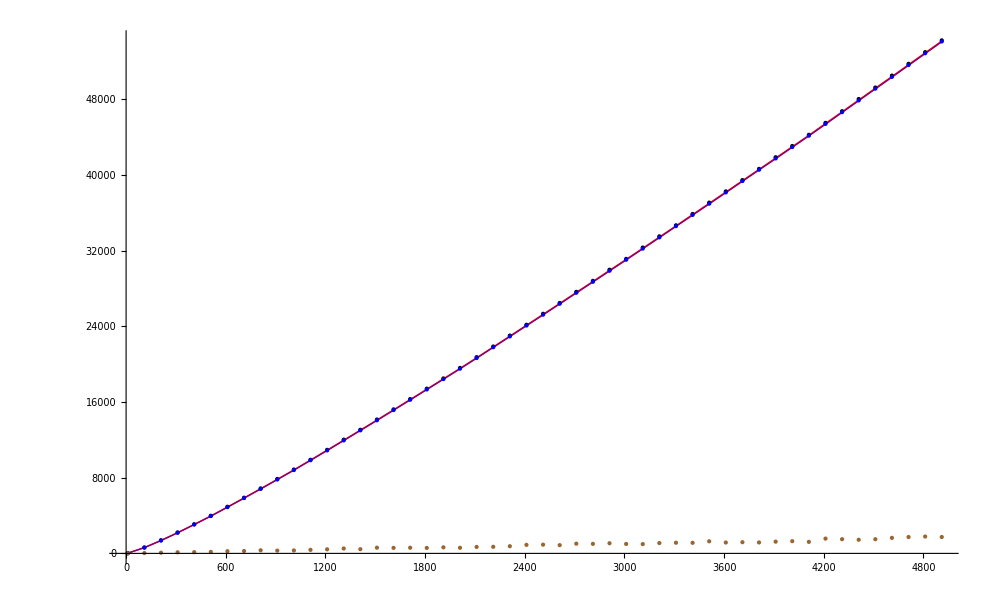

```mathematica
Show[
ListLinePlot[mergePlusStandardDeviation,PlotStyle->Red],
ListLinePlot[mergeMinusStandardDeviation,PlotStyle->Purple],
ListPlot[mergeMax,PlotStyle -> Black],
ListPlot[mergeMean,PlotStyle -> Blue],
ListPlot[mergeVariance, PlotStyle->Brown]
]
```

Wyświetlanie wyników dla QuickSorta:

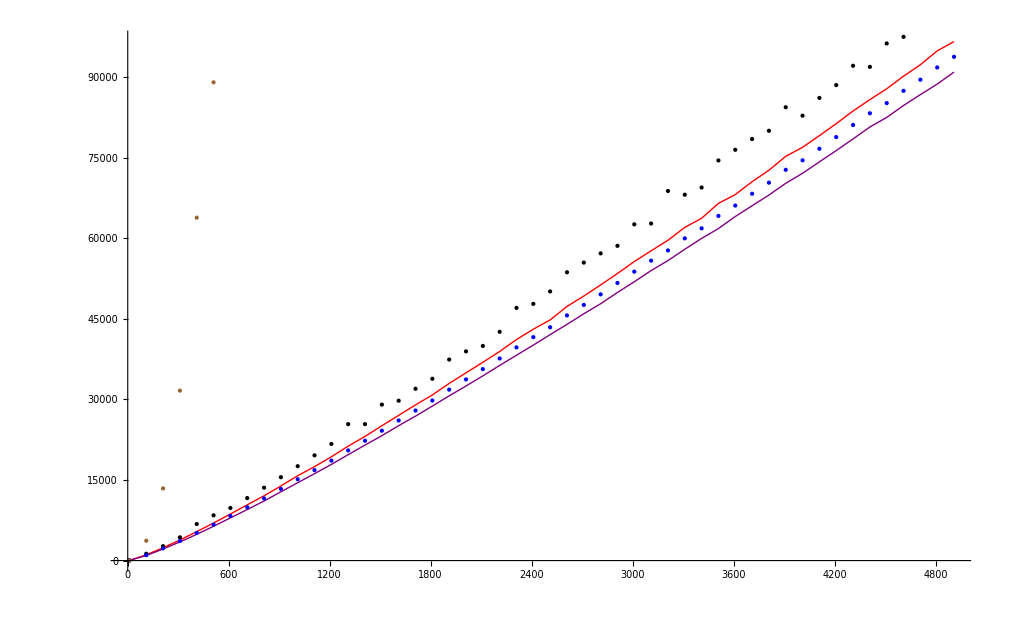

```mathematica
Show[
ListLinePlot[quickPlusStandardDeviation,PlotStyle->Red],
ListLinePlot[quickMinusStandardDeviation,PlotStyle->Purple],
ListPlot[quickMax,PlotStyle -> Black],
ListPlot[quickMean,PlotStyle -> Blue],
ListPlot[quickVariance, PlotStyle->Brown]
]
```

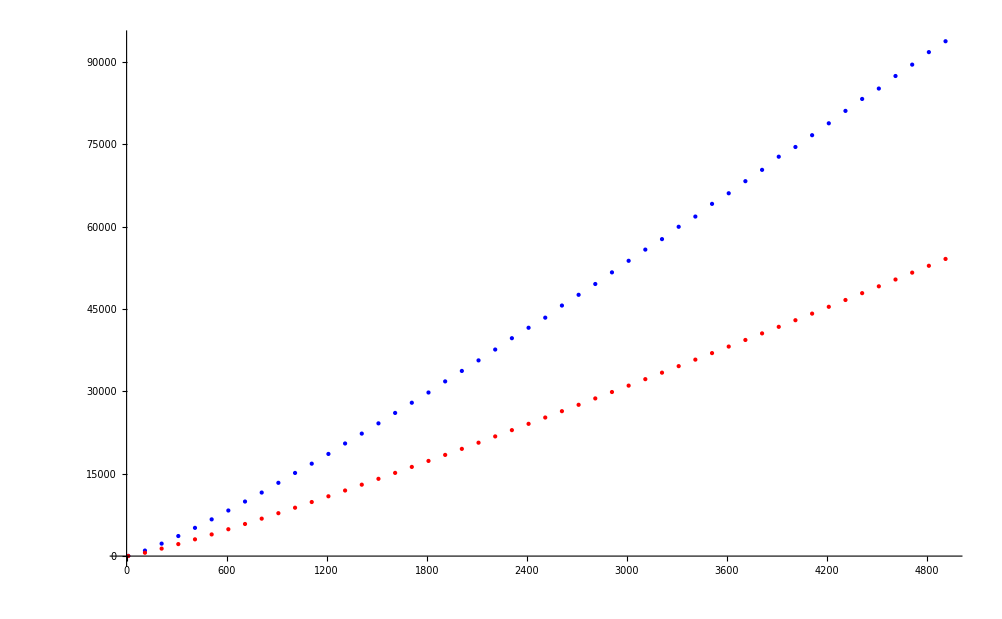

```mathematica
Show[
ListPlot[quickMean,PlotStyle -> Blue],
ListPlot[mergeMean, PlotStyle->Red]
]
```